```mathematica
p1=-0.001834;p2=1.788;p3=49.19;
a[t_]=p1*t^2+p2*t+p3
```

49.19+1.788 t-0.001834 t^2

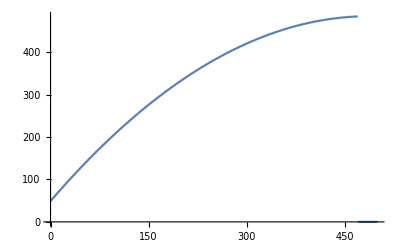

```mathematica
Plot[UnitStep[470-t]*a[t],{t,0,500}]
```

```mathematica
a0=1196;b1=-0.003154;c1=318.4;d1=-0.0007053;
b[t_]=a0*Exp[b1*t]+c1*Exp[d1*t]
```

1196 ⅇ^(-0.003154 t)+318.4 ⅇ^(-0.0007053 t)

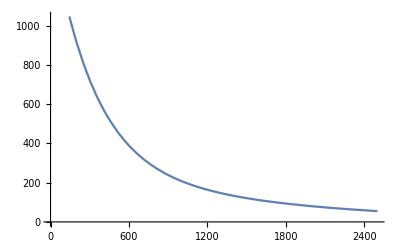

```mathematica
Plot[b[t],{t,0,2500}]
```

```mathematica
Plot[UnitStep[470-t]*a[t]+UnitStep[t-470]*b[t]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

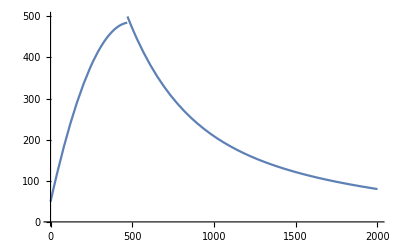

```mathematica
Plot[UnitStep[470-t] a[t]+UnitStep[t-470] b[t],{t,0,2000}]
```

```mathematica
LaplaceTransform[UnitStep[470-t] a[t]+UnitStep[t-470] b[t],t,s]
```

(1.788 ⅇ^(-470 s) (-1+ⅇ^(470 s)-470 s))/s^2+(49.19 (1-ⅇ^(-470 s)))/s+(318.4 ⅇ^(-470 (0.0007053+s)))/(0.0007053+s)+(1196 ⅇ^(-470 (0.003154+s)))/(0.003154+s)-(0.003668 ⅇ^(-470 s) (-1+ⅇ^(470 s)-470 s-110450 s^2))/s^3

```mathematica
T[s_]=(1.788 ⅇ^(-470 s) (-1+ⅇ^(470 s)-470 s))/s^2+(49.19 (1-ⅇ^(-470 s)))/s+(318.4 ⅇ^(-470 (0.0007053+s)))/(0.0007053+s)+(1196 ⅇ^(-470 (0.003154+s)))/(0.003154+s)-(0.003668 ⅇ^(-470 s) (-1+ⅇ^(470 s)-470 s-110450 s^2))/s^3;
```

```mathematica
FullSimplify[T[s]]
```

1/(s^3 (0.0007053+s) (0.003154+s))ⅇ^(-470 s) (8.15953×10^-9+s (0.0000140135+s (0.00234325+s (-1.0211+15.7524 s)))+ⅇ^(470 s) (-8.15953×10^-9+s (-0.0000101785+s (0.00334185+s (1.97784+49.19 s)))))

```mathematica
Tf[s]=TransferFunctionModel[FullSimplify[T[s]],s]
```

(-8.15953×10^-9+8.15953×10^-9 ⅇ^(-470. s)-0.0000101785 s+0.0000140135 ⅇ^(-470. s) s+0.00334185 s^2+0.00234325 ⅇ^(-470. s) s^2+1.97784 s^3-1.0211 ⅇ^(-470. s) s^3+49.19 s^4+15.7524 ⅇ^(-470. s) s^4)/(2.22452×10^-6 s^3+0.0038593 s^4+s^5)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11-8.159525421599998e-92.2245162e-61FalseFalseFalseAutomaticNoneAutomatic

```mathematica
BodePlot[%49]
```